```mathematica
n=4;
k = 2;

(X=Table[x^i,{i, n},{1}])//MatrixForm
(S = Table[Subscript[s, j]^i,{j,k},{i, n}])//MatrixForm
(Y= Table[Subscript[y, j],{j,k},{1}])//MatrixForm
(Id = IdentityMatrix[n])//MatrixForm
```

(x
x^2
x^3
x^4)

(s_1 | s_1^2 | s_1^3 | s_1^4
s_2 | s_2^2 | s_2^3 | s_2^4)

(y_1
y_2)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(X =DiagonalMatrix[Flatten@X])//MatrixForm
```

(x | 0 | 0 | 0
0 | x^2 | 0 | 0
0 | 0 | x^3 | 0
0 | 0 | 0 | x^4)

```mathematica
{Y//MatrixForm,S.X//MatrixForm}
```

{(y_1
y_2),(x s_1 | x^2 s_1^2 | x^3 s_1^3 | x^4 s_1^4
x s_2 | x^2 s_2^2 | x^3 s_2^3 | x^4 s_2^4)}

```mathematica
n=Sqrt[Times@@Dimensions@X];(X = 1-ExampleData[{"TestImage", "ResolutionChart"}]//ImageData)//Image
```

-Graphics-

```mathematica
δ[u_,v_,ϕ_]:= SparseArray[{u,v}->ⅇ^(ⅈ*ϕ),Dimensions@X];
P[u_,v_,ϕ_]:=n/2(1+Re@InverseFourier[δ[u,v,ϕ]]);
(S=P[20,2,π]-P[20,2,0])//MatrixPlot[#,PlotLegends->Automatic]&
(Y = (Abs@Fourier[S*X]))//MatrixPlot[#,PlotLegends->Automatic]&
```

-Graphics-

-Graphics-

```mathematica
Re@InverseFourier@δ[100, 100, π]//Min
```

-0.00390625

```mathematica
FourierMatrix[2]//MatrixForm
Fourier/@({{1, 0}, {0, 1}})//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

(0.707107 | 0.707107
0.707107 | -0.707107)

3

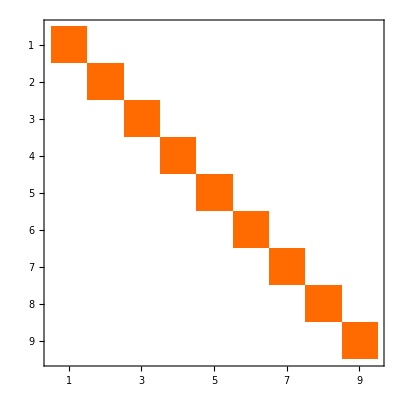

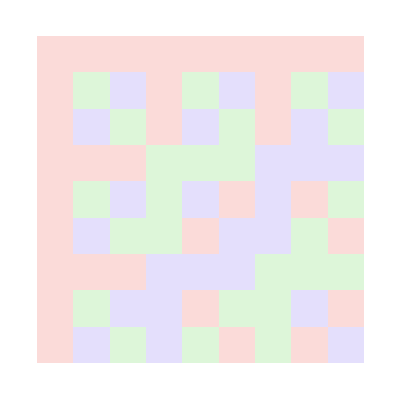

```mathematica
(* 2D fourier transform matrix, flattend *)
n=3
Flatten[Table[Flatten@SparseArray[{i,j}->1, {n,n}],{i,n}, {j,n}],1]//MatrixPlot
(F1 = Flatten[Table[Flatten@Fourier@SparseArray[{i,j}->1, {n,n}],{i,n}, {j,n}],1])//ComplexArrayPlot[#, PlotLegends->Automatic]&
```

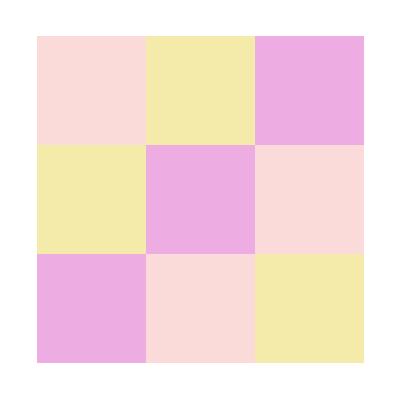
{-Graphics-,-Graphics-}

```mathematica
test= ({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}});
{
F1.Flatten@test//ArrayReshape[#,{3,3}]&//ComplexArrayPlot,
Fourier@test//ComplexArrayPlot
}
```

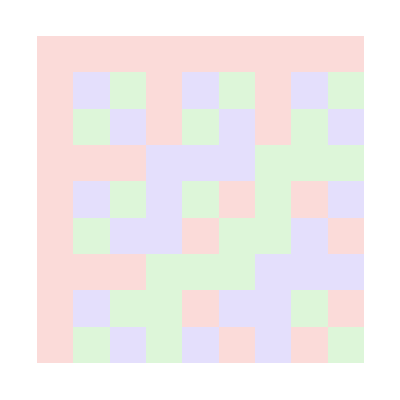
{-Graphics-,-Graphics-,-Graphics-}

False

```mathematica
{F1//ComplexArrayPlot,
Inverse@F1//ComplexArrayPlot,
Conjugate@F1//ComplexArrayPlot
}
Inverse@F1==Conjugate@F1 (* should be true, but there's floating point error *)
```

{(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)}

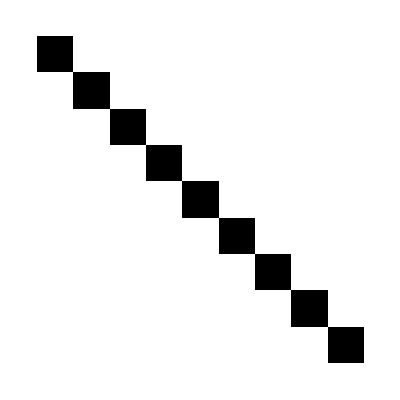

-Graphics-

```mathematica
n=3;
basis[n_] :=ArrayReshape[IdentityMatrix[n*n],{n*n, n,n}]
(basis[n][[#]]//MatrixForm)&/@{1,2, 3, 9}
List/@basis[n]//ArrayReshape[#,{n*n,n*n}]&//ArrayPlot
Fourier/@basis[n]//ArrayReshape[#,{n*n,n*n}]&//ComplexArrayPlot
```

```mathematica
ArrayResample[#,2,{"Bin",0},Resampling->"Linear"]&/@ArrayReshape[IdentityMatrix[9],{9, 3,3}]
Image/@%
```

{{{9/16,0},{0,0}},{{3/16,3/16},{0,0}},{{0,9/16},{0,0}},{{3/16,0},{3/16,0}},{{1/16,1/16},{1/16,1/16}},{{0,3/16},{0,3/16}},{{0,0},{9/16,0}},{{0,0},{3/16,3/16}},{{0,0},{0,9/16}}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
resampleMatrix[m_,n_]:=
Flatten/@(ArrayResample[#,m,"Bin",Resampling->"Linear",Padding->0]&/@ArrayReshape[IdentityMatrix[n*n],{n*n,n,n}])
MatrixForm/@resampleMatrix[2,3]//N
resampleMatrix[2,3]//Dimensions
```

```mathematica
(ArrayResample[#,2,"Bin",Resampling->"Linear",Padding->0]&/@ArrayReshape[IdentityMatrix[9],{9,3,3}])//Dimensions
```

{9,2,2}

```mathematica
resampleMatrix[2,3]//Dimensions
```

{9,4}

```mathematica
PseudoInverse@resampleMatrix[2,4].resampleMatrix[2,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
resampleMatrix[4,2].PseudoInverse@resampleMatrix[4,2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
resampleMatrix[2,3]//Dimensions
```

{9,4}

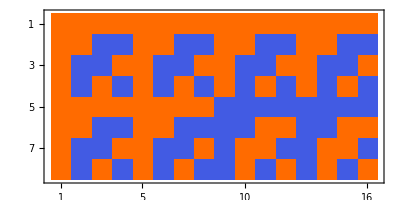

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(maskFull=Flatten/@DiscreteHadamardTransform/@ArrayReshape[IdentityMatrix[16],{16,4,4}])//MatrixPlot;
(mask=maskFull[[1;;8]])//MatrixPlot
mask.PseudoInverse@mask//MatrixForm
```

```mathematica
S=mask;
1-ExampleData[{"TestImage", "ResolutionChart"}]//ImageResize[#,{4,4}]&
X = Flatten@ImageData@%;
Y =S.X
PseudoInverse[S].Y//ArrayReshape[#,{4,4}]&//Image
```

-Graphics-

{0.455946,0.0311919,-0.182434,-0.0195213,0.0436507,0.00230124,-0.0835891,0.0149275}

-Graphics-

```mathematica
PseudoInverse[S]==Sᵀ.Inverse[S.Sᵀ]
S.PseudoInverse[S]==IdentityMatrix[Dimensions[S][[1]]]
S.Sᵀ==IdentityMatrix[Dimensions[S][[1]]]

S.PseudoInverse[S].Y==S.X
```

True

True

True

«1 more identical outputs»

```mathematica
X={3/4,3/4,1/4,1/4}
DiscreteHadamardTransform[X]
S={DiscreteHadamardTransform[{1,0,0,0}], DiscreteHadamardTransform[{0,1,0,0}]}
Y = S.X
PseudoInverse[S].Y
Sᵀ.Y
```

{3/4,3/4,1/4,1/4}

{1,1/2,0,0}

{{1/2,1/2,1/2,1/2},{1/2,1/2,-1/2,-1/2}}

{1,1/2}

{3/4,3/4,1/4,1/4}

{3/4,3/4,1/4,1/4}

```mathematica
δ =IdentityMatrix[4] 
H = DiscreteHadamardTransform/@δ
S={DiscreteHadamardTransform[{1,0,0,0}], DiscreteHadamardTransform[{0,1,0,0}]}
S.H
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{1/2,1/2,1/2,1/2},{1/2,1/2,-1/2,-1/2},{1/2,-1/2,-1/2,1/2},{1/2,-1/2,1/2,-1/2}}

{{1/2,1/2,1/2,1/2},{1/2,1/2,-1/2,-1/2}}

{{1,0,0,0},{0,1,0,0}}